# Mutualistic system - adaptive dynamics

```mathematica
(* The mutualistic system: *)
```

```mathematica
fA[ α_]:= A (rA-cA A + α gP P)
```

```mathematica
fP[α_]:= P(rP[α]-cP P + α gA A)
```

```mathematica
equation = Solve[{fA[α] == 0,fP[α] == 0},{A,P}]// FullSimplify
```

{{A→0,P→rP[α]/cP},{A→(cP rA+gP α rP[α])/(cA cP-gA gP α^2),P→(gA rA α+cA rP[α])/(cA cP-gA gP α^2)},{A→0,P→0},{A→rA/cA,P→0}}

```mathematica
Aeqs[α_]=(A/. equation)[[2]]//FullSimplify
```

(cP rA+gP α rP[α])/(cA cP-gA gP α^2)

```mathematica
Peqs[α_]=(P/. equation)[[2]]//FullSimplify
```

(gA rA α+cA rP[α])/(cA cP-gA gP α^2)

```mathematica
(*expression of the fitness function*)
```

```mathematica
w[αm_,α_]=rP[αm]-cP Peqs[α]+αm gA Aeqs[α];
```

```mathematica
(* Calculation of the first derivation with αm*)
```

```mathematica
dwdαm[αm_,α_]=D[w[αm,α],αm]
```

(gA (cP rA+gP α rP[α]))/(cA cP-gA gP α^2)+rP'[αm]

```mathematica
(* Calculation of the second derivation with αm *)
```

```mathematica
d2wdαm2[αm_,α_]=D[dwdαm[αm,α],αm]
```

rP''[αm]

```mathematica
(* Calculation of the cross derivation *)
```

```mathematica
d2wdαmdα[αm_,α_]=(D[dwdαm[αm,α],α]//FullSimplify)
```

(gA gP (2 cP gA rA α+(cA cP+gA gP α^2) rP[α]+(cA cP α-gA gP α^3) rP'[α]))/(cA cP-gA gP α^2)^2

```mathematica
D[gA*Aeqs[α],α]//FullSimplify
```

(gA gP (2 cP gA rA α+(cA cP+gA gP α^2) rP[α]+(cA cP α-gA gP α^3) rP'[α]))/(cA cP-gA gP α^2)^2

```mathematica
Myd2wdαmdα[αm_,α_]=(gA gP (2 cP gA rA α+(cA cP+gA gP α^2)( rP[α]+αrP'[α])))/(cA cP-gA gP α^2)^2
```

(gA gP (2 cP gA rA α+(cA cP+gA gP α^2) (rP[α]+αrP'[α])))/(cA cP-gA gP α^2)^2

```mathematica
Myd2wdαmdα[αm,α]- d2wdαmdα[αm,α]//Expand//FullSimplify
```

(gA gP ((-cA cP α+gA gP α^3) rP'[α]+(cA cP+gA gP α^2) αrP'[α]))/(cA cP-gA gP α^2)^2

## Simplest fitness function : rP + α= 1

```mathematica
rPf1[α_]=1-(α/αmax)
```

1-α/αmax

```mathematica
D[rPf1[α],α]
```

-1/αmax

```mathematica
(* replace rP in the first derivation by its function: *)
```

```mathematica
wf1[αm_,α_]= w[αm,α]/.{rP-> rPf1}
```

1-(cP (gA rA α+cA (1-α/αmax)))/(cA cP-gA gP α^2)+(gA αm (cP rA+gP α (1-α/αmax)))/(cA cP-gA gP α^2)-αm/αmax

```mathematica
dwf1dαm[αm_,α_]=D[wf1[αm,α],αm]
```

(gA (cP rA+gP α (1-α/αmax)))/(cA cP-gA gP α^2)-1/αmax

```mathematica
αeq1=Values[Solve[dwf1dαm[α,α]==0,α]//FullSimplify//Flatten][[1]]
```

(cP (cA-gA rA αmax))/(gA gP αmax)

```mathematica
Reduce[αeq1>0&&gA>0&&gP>0&&cA>0&&cP>0&&rA>0&&α>0&&α<αmax&&(α^2) gA gP< (cA cP)&&0<αmax<Sqrt[(cP*cA)/(gP*gA)], rA,Reals]
```

αmax>0&&0<α<αmax&&gP>0&&cP>0&&cA>0&&0<gA<(cA cP)/(gP αmax^2)&&0<rA<cA/(gA αmax)

```mathematica
paramPIPrA05 = {cP ->1,cA->1,gA->1,gP->1,rA->0.5};
```

```mathematica
αcl=Sqrt[(cP*cA)/(gP*gA)];
```

```mathematica
cA/(gA αmax)/.αmax->0.8*αcl/.paramPIPrA05
```

1.25

The singular strategy is feasible (αeq > 0)

```mathematica
(cP (cA-gA rA αmax))/(gA gP αmax)/.αmax->0.8*αcl/.paramPIPrA05
```

0.75

Its value correspond to the PIP plotted with the same parameter values

```mathematica
(*For the cross derivation*)
```

```mathematica
d2wf1dαmdα[αm_,α_]=(D[dwf1dαm[αm,α],α]//FullSimplify)
```

(gA gP (gA α (2 cP rA+gP α) αmax+cA cP (-2 α+αmax)))/((cA cP-gA gP α^2)^2 αmax)

```mathematica
(* Can I further factorise the result? *)
```

```mathematica
myd2wf1dαmdα[αm_,α_]=(gA gP (cA cP (-2 α/αmax+1)+α  gA (α gP+2 cP rA)))/(cA cP-α^2 gA gP)^2
```

(gA gP (gA α (2 cP rA+gP α)+cA cP (1-(2 α)/αmax)))/((cA cP-gA gP α^2)^2)

```mathematica
myd2wf1dαmdα[αm,α]-d2wf1dαmdα[αm,α]//FullSimplify
```

0

```mathematica
d2wf1dαm2[αm_,α_]=(D[dwf1dαm[αm,α],αm]//FullSimplify)
```

0

```mathematica
Myd2wf1dαmdα[αm_,α_]=(gA gP (α^2 gA gP +2 cP α( rA gA - cA/αmax )+cA cP))/(cA cP-α^2 gA gP)^2
```

(gA gP (cA cP+gA gP α^2+2 cP α (gA rA-cA/αmax)))/((cA cP-gA gP α^2)^2)

```mathematica
Myd2wf1dαmdα[αm,α]-d2wf1dαmdα[αm,α]//FullSimplify
```

0

```mathematica
(* Is the sum of both second and cross derivation always negative ? *)
```

```mathematica
Reduce[(Myd2wf1dαmdα[α,α])>0&&gA>0&&gP>0&&cA>0&&cP>0&&rA>0 &&αmax>α>0&&(α^2) gA gP< (cA cP)&&0<αmax<Sqrt[(cP*cA)/(gP*gA)], Reals, rA ]
```

αmax>0&&0<α<αmax&&gP>0&&cP>0&&cA>0&&0<gA<(cA cP)/(gP αmax^2)

```mathematica
Myd2wf1dαmdα[αeq1,αeq1]
```

(gA gP (cA cP+(2 cP^2 (gA rA-cA/αmax) (cA-gA rA αmax))/(gA gP αmax)+(cP^2 (cA-gA rA αmax)^2)/(gA gP αmax^2)))/(cA cP-(cP^2 (cA-gA rA αmax)^2)/(gA gP αmax^2))^2

```mathematica
Myd2wf1dαmdα[αeq1,αeq1]//FullSimplify
```

-((gA^2 gP^2 αmax^2)/(cP (cA^2 cP+cP gA^2 rA^2 αmax^2-cA gA αmax (2 cP rA+gP αmax))))

```mathematica
Reduce[(Myd2wf1dαmdα[αeq1,αeq1]//FullSimplify)<0&&gA>0&&gP>0&&cA>0&&cP>0&&rA>0&&α>0&&α<αmax&&(α^2) gA gP< (cA cP)&&0<αmax<Sqrt[(cP*cA)/(gP*gA)],rA, Reals ]
```

αmax>0&&0<α<αmax&&gP>0&&cP>0&&cA>0&&0<gA<(cA cP)/(gP αmax^2)&&(0<rA<-√((cA gP)/(cP gA))+cA/(gA αmax)||rA>√((cA gP)/(cP gA))+cA/(gA αmax))

## Fitness function : rP^δ + e^δ = 1

```mathematica
Clear[αmax]
```

```mathematica
αcl=Sqrt[(cP*cA)/(gP*gA)];
```

```mathematica
rPf2[α_]:=(1-(α/αcl)^s)^(1/s);
```

```mathematica
rPf3[α_]:=(1-(α/αmax)^s)^(1/s);
```

```mathematica
rPf4[α_]:=(1-(α)^s)^(1/s);
```

```mathematica
drpf3dα[α_]=D[rPf3[α],α]//FullSimplify
```

-((1-(α/αmax)^s)^(-1+1/s) (α/αmax)^s)/α

```mathematica
drpf3dα[α]/rPf3[α]//FullSimplify
```

1/(α-α (α/αmax)^-s)

### With αmax below the critical level αcl

```mathematica
rPf4[α_]= (1-(α/(0.8*αcl))^s)^(1/s)
```

(1-1.25^s (α/(√((cA cP)/(gA gP))))^s)^(1/s)

```mathematica
wf4[αm_,α_]= w[αm,α]/.{rP-> rPf4}
```

-(cP (gA rA α+cA (1-1.25^s (α/(√((cA cP)/(gA gP))))^s)^(1/s)))/(cA cP-gA gP α^2)+(gA (cP rA+gP α (1-1.25^s (α/(√((cA cP)/(gA gP))))^s)^(1/s)) αm)/(cA cP-gA gP α^2)+(1-1.25^s (αm/(√((cA cP)/(gA gP))))^s)^(1/s)

### PIPs plots

```mathematica
(* in order to save nice looking PIPs *)
```

```mathematica
rasterTrick[plot_]:=Show[plot,Prolog->{Opacity[0],Texture[{{{0,0,0,0}}}],VertexTextureCoordinates->{{0,0},{1,0},{1,1}},Polygon[{{0,0},{.1,0},{.1,.1}}]}]
```

```mathematica
paramPIPrA05 = {cP ->1,cA->1,gA->1,gP->1,rA->0.5,s->0.5};
```

```mathematica
fullwf2rA05[αm_,α_]=wf2[αm,α]/.paramPIPrA05
```

-((1-α^0.5)^2.+0.5 α)/(1-α^2)+(1-αm^0.5)^2.+((0.5+(1-α^0.5)^2. α) αm)/(1-α^2)

```mathematica
αcl=Sqrt[cA cP/(gA gP)];
```

```mathematica
αmax=αcl*0.8;
```

```mathematica
fullαclrA05=αcl/.paramPIPrA05
```

1

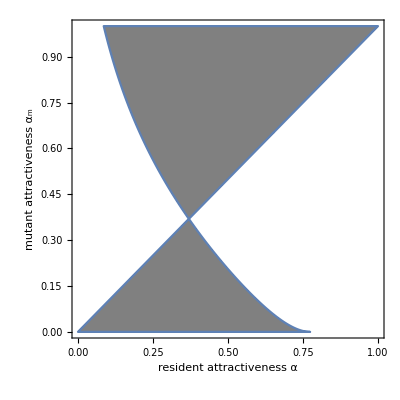

```mathematica
PIP2rA05 = RegionPlot[fullwf2rA05[αm,α]>0,{α,0,fullαclrA05}, {αm, 0, fullαclrA05}, PlotStyle->Gray, FrameStyle->Black, FrameLabel->{"resident attractiveness α","mutant attractiveness"Subscript[α,m]},LabelStyle->Directive[Black,FontSize->22],FrameTicksStyle->Directive[Black,22],PlotPoints->100]
```

```mathematica
Export[NotebookDirectory[]<>"PIPdelta2_rA05.jpg",PIP2rA05//rasterTrick];
```

#### With delta < 1

```mathematica
paramPIPrA05D05= {cP->1,cA->1,gA->1,gP->1,rA->0.5,s->0.5}
```

{cP→1,cA→1,gA→1,gP→1,rA→0.5,s→0.5}

```mathematica
fullwf4rA05D05[αm_,α_]=wf4[αm,α]/.paramPIPrA05D05
```

-((1-1.11803 α^0.5)^2.+0.5 α)/(1-α^2)+(1-1.11803 αm^0.5)^2.+((0.5+(1-1.11803 α^0.5)^2. α) αm)/(1-α^2)

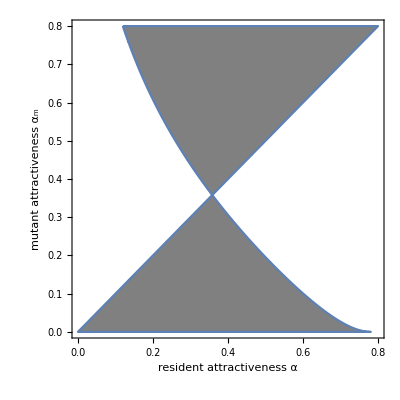

```mathematica
PIP4rA05D05 = RegionPlot[fullwf4rA05D05[αm,α]>0,{α,0,0.8*fullαclrA05}, {αm, 0, 0.8*fullαclrA05}, PlotStyle->Gray, FrameStyle->Black, FrameLabel->{"resident attractiveness α","mutant attractiveness"Subscript[α,m]},LabelStyle->Directive[Black,FontSize->22],FrameTicksStyle->Directive[Black,22],PlotPoints->200]
```

```mathematica
Export[NotebookDirectory[]<>"PIPD05rP08aclrA05_rA05.jpg",PIP4rA05D05//rasterTrick]
```

/home/avril/Adaptive_dynamics/mathematica/PIPD05rP08aclrA05_rA05.jpg

#### With a linear tradeoff

```mathematica
paramPIPrA05s1= {cP->1,cA->1,gA->1,gP->1,rA->0.5,s->1}
```

{cP→1,cA→1,gA→1,gP→1,rA→0.5,s→1}

```mathematica
fullwf4rA05s1[αm_,α_]=wf4[αm,α]/.paramPIPrA05s1
```

1-(1-0.75 α)/(1-α^2)-1.25 αm+((0.5+(1-1.25 α) α) αm)/(1-α^2)

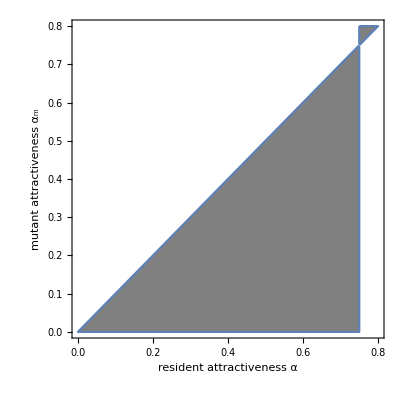

```mathematica
PIP4rA05s1 = RegionPlot[fullwf4rA05s1[αm,α]>0,{α,0,0.8*fullαclrA05}, {αm, 0, 0.8*fullαclrA05}, PlotStyle->Gray, FrameStyle->Black, FrameLabel->{"resident attractiveness α","mutant attractiveness"Subscript[α,m]},LabelStyle->Directive[Black,FontSize->22],FrameTicksStyle->Directive[Black,22],PlotPoints->100]
```

```mathematica
Export[NotebookDirectory[]<>"PIPs1rP08aclrA05.jpg",PIP4rA05s1//rasterTrick]
```

/home/avril/Adaptive_dynamics/mathematica/PIPs1rP08aclrA05.jpg

#### With a concave tradeoff

```mathematica
paramPIPrA05={cP->1,cA->1,gA->1,gP->1,rA->0.5}
```

{cP→1,cA→1,gA→1,gP→1,rA→0.5}

```mathematica
fullwf4rA05d3[αm_,α_]=wf4[αm,α]/.paramPIPrA05/.s-> 3
```

-(0.5 α+(1-1.95313 α^3)^(1/3))/(1-α^2)+((0.5+α (1-1.95313 α^3)^(1/3)) αm)/(1-α^2)+(1-1.95313 αm^3)^(1/3)

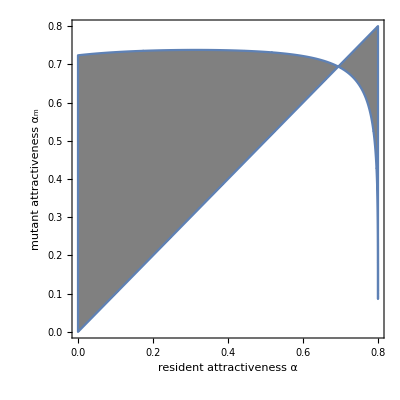

```mathematica
PIP4rA05=RegionPlot[fullwf4rA05d3[αm,α]>0,{α,0,0.8 fullαclrA05},{αm,0,0.8 fullαclrA05},PlotStyle->Gray,FrameStyle->Black,FrameLabel->{"resident attractiveness α","mutant attractiveness" Subscript[α, m]},LabelStyle->Directive[Black,FontSize->22],FrameTicksStyle->Directive[Black,22],PlotPoints->100]
```

```mathematica
Export[NotebookDirectory[]<>"PIPD3rP08αclrA05.jpg",PIP4rA05//rasterTrick]
```

/home/avril/Adaptive_dynamics/mathematica/PIPD3rP08αclrA05.jpg

#### With rA < 0

```mathematica
paramPIPrA05
```

{cP→1,cA→1,gA→1,gP→1,rA→0.5}

```mathematica
paramPIPrAm01s3= {cP->1,cA->1,gA->1,gP->1,rA->-0.1,s->3}
```

{cP→1,cA→1,gA→1,gP→1,rA→-0.1,s→3}

```mathematica
fullwf4rAm01[αm_,α_]=wf4[αm,α]/.paramPIPrAm01s3
```

-(-0.1 α+(1-1.95313 α^3)^(1/3))/(1-α^2)+((-0.1+α (1-1.95313 α^3)^(1/3)) αm)/(1-α^2)+(1-1.95313 αm^3)^(1/3)

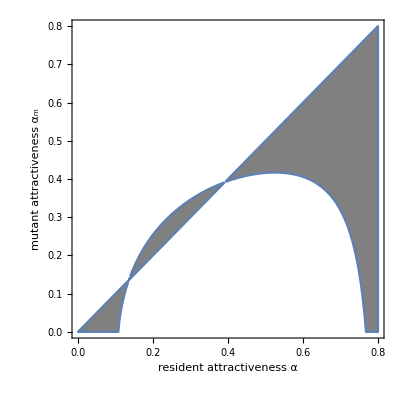

```mathematica
PIP4rAm01d3 = RegionPlot[fullwf4rAm01[αm,α]>0,{α,0,0.8*fullαclrA05}, {αm, 0, 0.8*fullαclrA05}, PlotStyle->Gray, FrameStyle->Black, FrameLabel->{"resident attractiveness α","mutant attractiveness"Subscript[α,m]},LabelStyle->Directive[Black,FontSize->22],FrameTicksStyle->Directive[Black,22],PlotPoints->100]
```

```mathematica
Export[NotebookDirectory[]<>"PIPD3rP08aclrAm01.jpg",PIP4rAm01d3//rasterTrick]
```

/home/avril/Adaptive_dynamics/mathematica/PIPD3rP08aclrAm01.jpg